```mathematica
(* Need to get the notes of the scales*)
(*Need to define the particles, fermions verus bosons*) 
(*create mapping*)
(*define function that maps graph to music*)
An[n_]:=EmitSound[SoundNote["A", n, "Violin"]]
Bn[m_]:=EmitSound[SoundNote["B", m, "Violin"]]
As[m1_]:=EmitSound[SoundNote["ASharp", m1, "Violin"]]
Cn[m2_]:=EmitSound[SoundNote["C", m2, "Violin"]]
Cs[m3_]:=EmitSound[SoundNote["CSharp", m3, "Violin"]]
Dn[m4_]:=EmitSound[SoundNote["D", m4, "Violin"]]
Ds[m5_]:=EmitSound[SoundNote["DSharp", m5, "Violin"]]
En[m6_]:=EmitSound[SoundNote["E", m6, "Violin"]]
Fn[m7_]:=EmitSound[SoundNote["F", m7, "Violin"]]
Fs[m8_]:=EmitSound[SoundNote["FSharp", m8, "Violin"]]
Gn[m9_]:=EmitSound[SoundNote["G", m9, "Violin"]]
Gs[m10_]:=EmitSound[SoundNote["GSharp", m10, "Violin"]]
HotCrossBuns:= Fs[1]+En[1]+Dn[1]+ Fs[1]+En[1]+Dn[1]+Dn[1]+Dn[1]+Dn[1]+Dn[1]+En[1]+En[1]+En[1]+En[1]+ Fs[1]+En[1]+Dn[1]

ChrS:={An, As, Bn, Cn, Cs, Dn, Ds, En, Fn, Fs, Gn, Gs}
(*Watch the chords while I define the relations*)
DimSecond[a_]:=If[a<12, a+1, 1];
Second[b_]:=If[b<11, b+2,   1+Mod[b+1, 12]];
DimThird[c_]:=If[c<10, c+3, 1+Mod[c+2, 12]];
Third[d_]:=If[d<9, d+4, 1+Mod[d+3, 12]];
Fourth[e_]:=If[e<8, e+5, 1+Mod[e+4, 12]];
DimFifth[f_]:=If[f<7, f+6, 1+Mod[f+5, 12]];
Fifth[g_]:=If[g<6, g+7, 1+Mod[g+6, 12]];
DimSixth[h_]:=If[h<5, h+8, 1+Mod[h+7, 12]];
Sixth[i_]:=If[i<4, i+9, 1+Mod[i+8, 12]];
DimSeventh[j_]:=If[j<3, j+10, 1+Mod[j+9, 12]];
Seventh[k_]:=If[k<2, k+11, 1+Mod[k+10, 12]];

(*These are the generic relations for the scales*)

(*This is the rule for a single group/chord*)
NoNeut[l_]:={ChrS⟦l⟧, ChrS⟦Third[l]⟧, ChrS⟦Fifth[l]⟧}
(*This is the group of the nine fermions w/out neutrinos*)
BaseGroup[w_,x_, o_]={NoNeut[w], NoNeut[x], NoNeut[o]}
NotesLeftOver[p_, q_, r_]:=Complement[ChrS, Flatten[BaseGroup[p, q, r]]]
```

Part::pkspec1: The expression w cannot be used as a part specification.

Part::pkspec1: The expression If[w<9,w+4,1+(] cannot be used as a part specification.

Part::pkspec1: The expression If[w<6,w+7,1+(] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

({An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦w⟧ | {An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦If[w<9,w+4,(w+3)12+1]⟧ | {An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦If[w<6,w+7,(w+6)12+1]⟧
{An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦x⟧ | {An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦If[x<9,x+4,(x+3)12+1]⟧ | {An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦If[x<6,x+7,(x+6)12+1]⟧
{An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦o⟧ | {An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦If[o<9,o+4,(o+3)12+1]⟧ | {An,As,Bn,Cn,Cs,Dn,Ds,En,Fn,Fs,Gn,Gs}⟦If[o<6,o+7,(o+6)12+1]⟧)

```mathematica
NotesLeftOver[1,2,3]
```

{Cn,Gn,Gs}

```mathematica
Leftoverwithindex:=MapThread[{NotesLeftOver[x,y,z], x,y,z},{{x, 1, 10,1}, {y, x+1, 11, 1}, {z, y+1, 12, 1}}]
```

```mathematica
SeventhRule[s_]:={Flatten[NoNeut[s]], ChrS⟦Seventh[s]⟧}
```

```mathematica
NotesLeftfromS[t_, u_, v_]:=Complement[ChrS, Flatten[{SeventhRule[t], SeventhRule[u], SeventhRule[v]}]]
```

```mathematica
ProofofNoSeventh:=Array[NotesLeftfromS, {12, 12, 12}]
```

```mathematica
Seventhdata:=Flatten[ProofofNoSeventh,2]
```

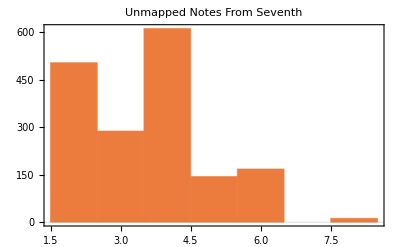

```mathematica
Histogram[Length/@Seventhdata⟦1;;Length[Seventhdata]⟧,PlotTheme->"Scientific", PlotLabel->HoldForm[Unmapped Notes From Seventh] ]
```

```mathematica
(*Now I need to do this on all the remaining, I think this would be a through not sure though*)
```